```mathematica
x={x1,x2,x3};y={x1,x2,x3+u[x1,x2]};
y//MatrixForm
```

(x1
x2
x3+u[x1,x2])

```mathematica
F={{D[y[[1]],x[[1]]],D[y[[1]],x[[2]]],D[y[[1]],x[[3]]]},
{D[y[[2]],x[[1]]],D[y[[2]],x[[2]]],D[y[[2]],x[[3]]]},
{D[y[[3]],x[[1]]],D[y[[3]],x[[2]]],D[y[[3]],x[[3]]]}};
F//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
u^(1,0)[x1,x2] | u^(0,1)[x1,x2] | 1)

```mathematica
Ca=Table[Sum[F[[i]][[a]]F[[i]][[b]],{i,1,3}],{a,1,3},{b,1,3}];
Ca//MatrixForm
```

(1+(u^(1,0)[x1,x2])^2 | u^(0,1)[x1,x2] u^(1,0)[x1,x2] | u^(1,0)[x1,x2]
u^(0,1)[x1,x2] u^(1,0)[x1,x2] | 1+(u^(0,1)[x1,x2])^2 | u^(0,1)[x1,x2]
u^(1,0)[x1,x2] | u^(0,1)[x1,x2] | 1)

```mathematica
I1=Tr[Ca];
```

```mathematica
P=Table[2 w' F[[i]][[a]] - p Inverse[F][[a]][[i]],{i,1,3},{a,1,3}];
```

```mathematica
P[[1]][[1]]=0;P[[1]][[2]]=0;
P[[3]][[3]]=0;P[[2]][[1]]=0;
P[[2]][[2]]=0;P[[1]][[3]]=P[[3]][[1]];
P[[2]][[3]]=P[[3]][[2]];
```

```mathematica
P//MatrixForm
```

(0 | 0 | 2 w' u^(1,0)[x1,x2]
0 | 0 | 2 w' u^(0,1)[x1,x2]
2 w' u^(1,0)[x1,x2] | 2 w' u^(0,1)[x1,x2] | 0)

```mathematica
w[i_]:=mu/(2b) ((1 + b/n (i-3))^n-1)
```

```mathematica
2 D[w[i],i]
```

mu (1+(b (-3+i))/n)^(-1+n)

```mathematica
mu (1+(b (-3+I1))/n)^(-1+n)
```

mu (1+(b ((u^(0,1)[x1,x2])^2+(u^(1,0)[x1,x2])^2))/n)^(-1+n)

```mathematica
u=k x2;
```

```mathematica
mu (1+(b ((Derivative[0,1][u][x1,x2])^2+(Derivative[1,0][u][x1,x2])^2))/n)^(-1+n)
```

mu (1+(b (((k x2)^(0,1)[x1,x2])^2+((k x2)^(1,0)[x1,x2])^2))/n)^(-1+n)

```mathematica
mu (1+(b (D[u,x2]^2+D[u,x2]^2))/n)^(-1+n)
```

mu (1+(2 b k^2)/n)^(-1+n)

```mathematica
mu(1+ b/n k^2)^(n-1) k
```

k mu (1+(b k^2)/n)^(-1+n)

```mathematica
mu=1;b=1;
```

```mathematica
shear[n_,k_]:=mu(1+ b/n k^2)^(n-1)   k 
shear[n,k]
```

k (1+k^2/n)^(-1+n)

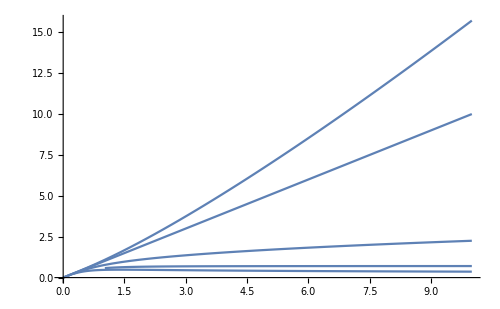

```mathematica
s1=Plot[shear[1.1,k],{k,0,10}];
s2=Plot[shear[1,k],{k,0,10}];
s3=Plot[shear[0.7,k],{k,0,10}];
s4=Plot[shear[0.5,k],{k,0,10}];
s5=Plot[shear[0.4,k],{k,0,10}];
Show[s1,s2,s3,s4,s5,ImageSize->500]
```